```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Marchevsky\VM2D\VM2Dcu4\settings\airfoils

```mathematica
n=3200;
```

```mathematica
Pts=N[Table[N[1/2{Cos[(2π)/n(i-1)],Sin[(2π)/n(i-1)]}],{i,1,n}],16];
```

```mathematica
Export
```

Export

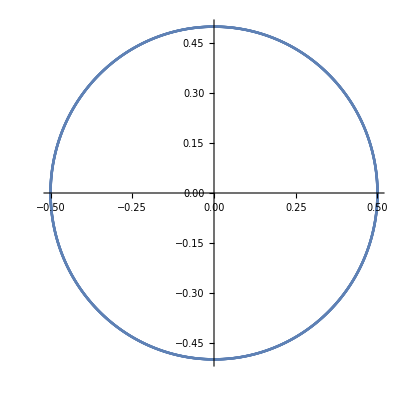

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
ToString[SetPrecision[Pts[[9]],17]]
```

{0.49993831624083029, 0.0078536586559103377}

```mathematica
Export["circle"<>ToString[n],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.3    |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2018/09/26     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2018 Ilia Marchevsky, Kseniia Kuzmina, Evgeniya Ryatina  |
*-----------------------------------------------------------------------------*
| File name: circle"<>ToString[n]<>StringRepeat[" ",59-StringLength@ToString[n]]<>"|
| Info: Circular airfoil ("<>ToString[n]<>" panels)"<>StringRepeat[" ",44-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"np = "<>ToString[n]<>";"}~Join~{"r = {"}~Join~((ToString[SetPrecision[#,17]]<>",")&/@(Pts[[1;;-2]]))~Join~((ToString[SetPrecision[#,17]])&/@(Pts[[{-1}]]))~Join~{" };"},"Table"]
```

circle3200